```mathematica
rawdata=Import[NotebookDirectory[]<>"MyFile.txt"];
```

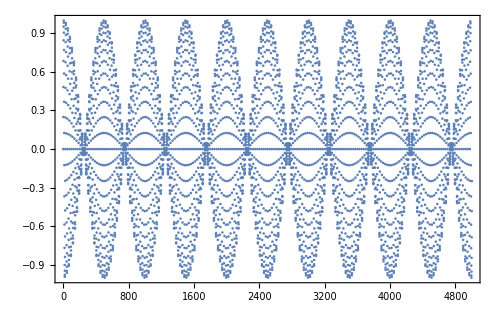

```mathematica
ListPlot[StringToExpression2/@StringSplit[rawdata,"\n"]]
```

```mathematica
trial1=StringToExpression2/@StringSplit[rawdata,"\n"];
```

```mathematica
trial2=StringToExpression2/@StringSplit[rawdata,"\n"];
```

```mathematica
Select[trial2,#==0&]
```

{0.}

```mathematica
Select[trial2,-0.0001<#<0.0001&]
```

{0.,1.2004×10^-14,-2.4008×10^-14,4.31175×10^-14,-4.80161×10^-14,5.29146×10^-14,-8.62349×10^-14,1.19555×10^-13,-9.60321×10^-14,1.56656×10^-14}

```mathematica
Select[trial1,-0.001<#<0.001&]
```

{0.,-6.80012×10^-16,-1.30451×10^-15,-6.66134×10^-16,-2.22045×10^-15,-2.10942×10^-15,-8.88178×10^-16,-3.9968×10^-15,-1.66533×10^-15,-8.88178×10^-16,0.,4.44089×10^-16,9.4369×10^-16,1.44329×10^-15,1.03806×10^-14,7.60503×10^-15,8.88178×10^-15,1.63758×10^-14,1.09635×10^-14,1.16157×10^-14,1.2004×10^-14,1.20876×10^-14,5.10703×10^-15,1.1352×10^-14,4.77396×10^-15,9.32587×10^-15,3.71925×10^-15,1.26565×10^-14,1.08802×10^-14,4.44089×10^-15,0.,-2.33147×10^-15,-6.82787×10^-15,-6.88338×10^-15,-2.15938×10^-14,-1.11022×10^-14,-1.86517×10^-14,-1.44051×10^-14,-2.2371×10^-14,-1.64591×10^-14,-2.4008×10^-14,-3.09752×10^-14,-2.33147×10^-14,-4.10227×10^-14,-8.71525×10^-15,-4.29656×10^-14,-1.4988×10^-14,-8.43769×10^-15,-3.66374×10^-15,-7.21645×10^-16,0.,-1.38778×10^-15,3.94129×10^-15,1.55431×10^-14,3.28071×10^-14,1.45439×10^-14,5.70655×10^-14,3.14193×10^-14,5.40401×10^-14,2.13024×10^-14,4.31175×10^-14,3.58047×10^-14,2.79776×10^-14,2.0095×10^-14,3.56382×10^-14,2.63678×10^-14,1.78746×10^-14,1.06581×10^-14,2.27041×10^-14,1.04361×10^-14,0.,-8.27116×10^-15,-1.42109×10^-14,-1.77636×10^-14,-1.89848×10^-14,-1.79856×10^-14,-3.80806×10^-14,-3.58047×10^-14,-3.16969×10^-14,-2.61319×10^-14,-4.80161×10^-14,-6.87228×10^-14,-5.96467×10^-14,-1.0042×10^-13,-3.96905×10^-14,-4.99045×10^-14,-5.41234×10^-14,0.,-6.66134×10^-15,-1.56541×10^-14,0.,4.60743×10^-15,1.57652×10^-14,3.29181×10^-14,2.19269×10^-14,1.38778×10^-15,1.90403×10^-14,9.08162×10^-14,9.32587×10^-15,3.09752×10^-14,5.29146×10^-14,7.35523×10^-14,-1.67921×10^-14,3.46945×10^-15,2.06501×10^-14,1.13687×10^-13,4.03566×10^-14,4.09117×10^-14,3.45279×10^-14,1.19904×10^-14,0.,-9.76996×10^-15,-4.36318×10^-14,-4.80171×10^-14,-4.14668×10^-14,-6.51146×10^-14,-9.1982×10^-14,-1.92069×10^-14,-4.0995×10^-14,-6.38795×10^-14,-8.62349×10^-14,-5.03347×10^-14,-6.89448×10^-14,-8.38218×10^-14,-4.75731×10^-14,-1.65978×10^-14,-2.64788×10^-14,-3.02536×10^-14,-2.7256×10^-14,-8.27116×10^-15,0.,6.10623×10^-15,1.87628×10^-14,1.15463×10^-14,2.7589×10^-14,8.87068×10^-14,1.18905×10^-13,9.95592×10^-14,1.2676×10^-13,9.67837×10^-14,6.27118×10^-14,8.3239×10^-14,1.00669×10^-13,1.13493×10^-13,7.4496×10^-14,8.03801×10^-14,4.60743×10^-14,4.54081×10^-14,1.9984×10^-14,1.34892×10^-14,0.,-2.02061×10^-14,-2.90878×10^-14,-5.25135×10^-14,-4.724×10^-14,-7.20535×10^-14,-5.39013×10^-14,-2.79221×10^-14,-5.02931×10^-14,-1.85837×10^-13,-9.60321×10^-14,-6.00076×10^-14,-1.32366×10^-13,-4.19109×10^-14,-1.01474×10^-13,-6.37268×10^-14,-1.32505×10^-13,-8.88178×10^-15,-3.03091×10^-14,-9.4369×10^-16,0.,7.66054×10^-15,5.69544×10^-14,4.17999×10^-14,0.,1.52656×10^-14,3.49165×10^-14,-4.36595×10^-14,1.90126×10^-13,2.18756×10^-13,2.43039×10^-13,1.49061×10^-13,5.58997×10^-14,1.72889×10^-13,8.24341×10^-14,8.7319×10^-14,8.52651×10^-14,7.56062×10^-14,2.30371×10^-14,1.4988×10^-14,0.,-2.17604×10^-14,-1.45439×10^-14,-8.27671×10^-14,-1.19793×10^-13,-1.59373×10^-13,-1.58207×10^-14,-1.37945×10^-13,-5.96467×10^-14,-1.95524×10^-13}

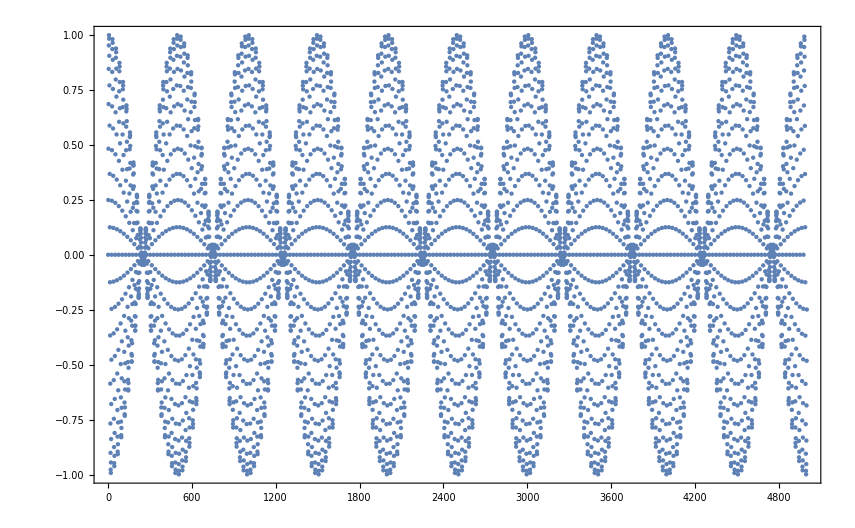

```mathematica
ListPlot[{trial1}]
```

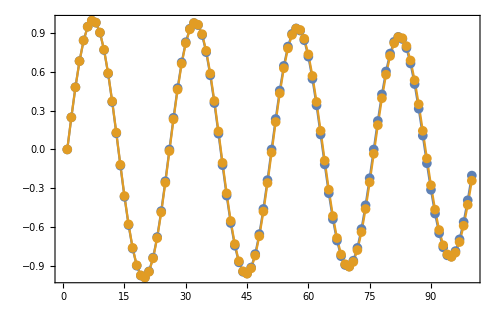

```mathematica
ListLinePlot[{trial1[[1;;100]],trial2[[1;;100]]},Mesh->All]
```